```mathematica
ClearAll["Global`*"]
```

```mathematica
F1[n_,1]:= F1[n,1]=Sum[ 2^k/k,{k,1,Log[2,n]}]
f1[n_,1] := f1[n,1]=F1[n,1]-F1[n-1,1]
f1[n_,k_] := f1[n,k]=F1[n,k]-F1[n-1,k]
f1[1,0] := 1
F1[n_,0]:=F1[n,0]=1
F1[n_, k_] := F1[n,k] = Sum[ f1[j,1]F1[Floor[n/j],k-1],{j,2,n}]
expf[n_] := Sum[ 1/(k!) f1[n,k],{k,0,Log[2,n]}]
Ex1[n_, 0] := 1; Ex1[n_, k_] := Ex1[n,k] = Sum[ expf[j] Ex1[ Floor[n/j], k-1],{j,1,n}]
ex1[n_, k_] := ex1[n,k]=Ex1[n,k]-Ex1[n-1,k]
Ex2[n_,k_] := Ex2[n,k]=Sum[(-1)^j Binomial[k,j] Ex1[n,k-j],{j,0,k}]
EF2[n_] := Sum[ (-1)^(k+1)/k Ex2[n,k],{k,1,Log[2,n]}]
```

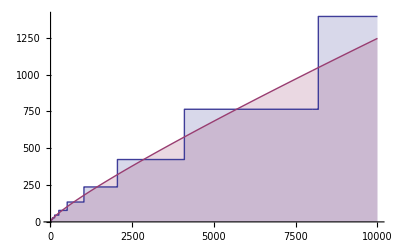

```mathematica
DiscretePlot[{F1[n,1],LogIntegral[n]},{n,2,10000}]
```

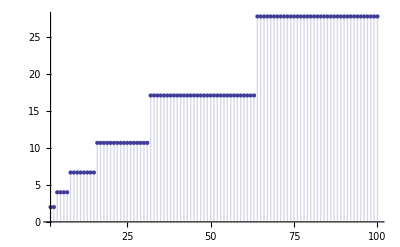

```mathematica
DiscretePlot[EF2[n],{n,2,100}]
```

```mathematica
Table[ {n,F1[n,1], EF2[n]},{n,1,100}]//TableForm
```

1 | 0 | 0
2 | 2 | 2
3 | 2 | 2
4 | 4 | 4
5 | 4 | 4
6 | 4 | 4
7 | 4 | 4
8 | 20/3 | 20/3
9 | 20/3 | 20/3
10 | 20/3 | 20/3
11 | 20/3 | 20/3
12 | 20/3 | 20/3
13 | 20/3 | 20/3
14 | 20/3 | 20/3
15 | 20/3 | 20/3
16 | 32/3 | 32/3
17 | 32/3 | 32/3
18 | 32/3 | 32/3
19 | 32/3 | 32/3
20 | 32/3 | 32/3
21 | 32/3 | 32/3
22 | 32/3 | 32/3
23 | 32/3 | 32/3
24 | 32/3 | 32/3
25 | 32/3 | 32/3
26 | 32/3 | 32/3
27 | 32/3 | 32/3
28 | 32/3 | 32/3
29 | 32/3 | 32/3
30 | 32/3 | 32/3
31 | 32/3 | 32/3
32 | 256/15 | 256/15
33 | 256/15 | 256/15
34 | 256/15 | 256/15
35 | 256/15 | 256/15
36 | 256/15 | 256/15
37 | 256/15 | 256/15
38 | 256/15 | 256/15
39 | 256/15 | 256/15
40 | 256/15 | 256/15
41 | 256/15 | 256/15
42 | 256/15 | 256/15
43 | 256/15 | 256/15
44 | 256/15 | 256/15
45 | 256/15 | 256/15
46 | 256/15 | 256/15
47 | 256/15 | 256/15
48 | 256/15 | 256/15
49 | 256/15 | 256/15
50 | 256/15 | 256/15
51 | 256/15 | 256/15
52 | 256/15 | 256/15
53 | 256/15 | 256/15
54 | 256/15 | 256/15
55 | 256/15 | 256/15
56 | 256/15 | 256/15
57 | 256/15 | 256/15
58 | 256/15 | 256/15
59 | 256/15 | 256/15
60 | 256/15 | 256/15
61 | 256/15 | 256/15
62 | 256/15 | 256/15
63 | 256/15 | 256/15
64 | 416/15 | 416/15
65 | 416/15 | 416/15
66 | 416/15 | 416/15
67 | 416/15 | 416/15
68 | 416/15 | 416/15
69 | 416/15 | 416/15
70 | 416/15 | 416/15
71 | 416/15 | 416/15
72 | 416/15 | 416/15
73 | 416/15 | 416/15
74 | 416/15 | 416/15
75 | 416/15 | 416/15
76 | 416/15 | 416/15
77 | 416/15 | 416/15
78 | 416/15 | 416/15
79 | 416/15 | 416/15
80 | 416/15 | 416/15
81 | 416/15 | 416/15
82 | 416/15 | 416/15
83 | 416/15 | 416/15
84 | 416/15 | 416/15
85 | 416/15 | 416/15
86 | 416/15 | 416/15
87 | 416/15 | 416/15
88 | 416/15 | 416/15
89 | 416/15 | 416/15
90 | 416/15 | 416/15
91 | 416/15 | 416/15
92 | 416/15 | 416/15
93 | 416/15 | 416/15
94 | 416/15 | 416/15
95 | 416/15 | 416/15
96 | 416/15 | 416/15
97 | 416/15 | 416/15
98 | 416/15 | 416/15
99 | 416/15 | 416/15
100 | 416/15 | 416/15

```mathematica
f1[1,0]
```

1

```mathematica
expf[1]
```

1

```mathematica
Ex1[1,1]
```

1

```mathematica
Table[ {n,Ex2[n,1], Ex2[n,2], Ex2[n,3]},{n,1,100}]//TableForm
```

1 | 0 | 0 | 0
2 | 2 | 0 | 0
3 | 2 | 0 | 0
4 | 6 | 4 | 0
5 | 6 | 4 | 0
6 | 6 | 4 | 0
7 | 6 | 4 | 0
8 | 14 | 20 | 8
9 | 14 | 20 | 8
10 | 14 | 20 | 8
11 | 14 | 20 | 8
12 | 14 | 20 | 8
13 | 14 | 20 | 8
14 | 14 | 20 | 8
15 | 14 | 20 | 8
16 | 30 | 68 | 56
17 | 30 | 68 | 56
18 | 30 | 68 | 56
19 | 30 | 68 | 56
20 | 30 | 68 | 56
21 | 30 | 68 | 56
22 | 30 | 68 | 56
23 | 30 | 68 | 56
24 | 30 | 68 | 56
25 | 30 | 68 | 56
26 | 30 | 68 | 56
27 | 30 | 68 | 56
28 | 30 | 68 | 56
29 | 30 | 68 | 56
30 | 30 | 68 | 56
31 | 30 | 68 | 56
32 | 62 | 196 | 248
33 | 62 | 196 | 248
34 | 62 | 196 | 248
35 | 62 | 196 | 248
36 | 62 | 196 | 248
37 | 62 | 196 | 248
38 | 62 | 196 | 248
39 | 62 | 196 | 248
40 | 62 | 196 | 248
41 | 62 | 196 | 248
42 | 62 | 196 | 248
43 | 62 | 196 | 248
44 | 62 | 196 | 248
45 | 62 | 196 | 248
46 | 62 | 196 | 248
47 | 62 | 196 | 248
48 | 62 | 196 | 248
49 | 62 | 196 | 248
50 | 62 | 196 | 248
51 | 62 | 196 | 248
52 | 62 | 196 | 248
53 | 62 | 196 | 248
54 | 62 | 196 | 248
55 | 62 | 196 | 248
56 | 62 | 196 | 248
57 | 62 | 196 | 248
58 | 62 | 196 | 248
59 | 62 | 196 | 248
60 | 62 | 196 | 248
61 | 62 | 196 | 248
62 | 62 | 196 | 248
63 | 62 | 196 | 248
64 | 126 | 516 | 888
65 | 126 | 516 | 888
66 | 126 | 516 | 888
67 | 126 | 516 | 888
68 | 126 | 516 | 888
69 | 126 | 516 | 888
70 | 126 | 516 | 888
71 | 126 | 516 | 888
72 | 126 | 516 | 888
73 | 126 | 516 | 888
74 | 126 | 516 | 888
75 | 126 | 516 | 888
76 | 126 | 516 | 888
77 | 126 | 516 | 888
78 | 126 | 516 | 888
79 | 126 | 516 | 888
80 | 126 | 516 | 888
81 | 126 | 516 | 888
82 | 126 | 516 | 888
83 | 126 | 516 | 888
84 | 126 | 516 | 888
85 | 126 | 516 | 888
86 | 126 | 516 | 888
87 | 126 | 516 | 888
88 | 126 | 516 | 888
89 | 126 | 516 | 888
90 | 126 | 516 | 888
91 | 126 | 516 | 888
92 | 126 | 516 | 888
93 | 126 | 516 | 888
94 | 126 | 516 | 888
95 | 126 | 516 | 888
96 | 126 | 516 | 888
97 | 126 | 516 | 888
98 | 126 | 516 | 888
99 | 126 | 516 | 888
100 | 126 | 516 | 888